```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
nmass=Length[mass];
number=3
npseudobin=20;
pvaluestandard=0.0455;
```

C:\Users\Lalu Zam\Documents\top-quark-thesis\mathematica

3

```mathematica
DATA FROM HELAC (FOR STANDARD PSEUDODATA GENERATOR);
```

```mathematica
file=Table[FileNames[][[i+5]],{i,1,nmass}];
nbins=20;

start[n_]:=2+(n-1)*nbins
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossection=Table[Reap[Do[Sow[data[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)
```

{951.072,930.023,906.377,882.921,859.732}

```mathematica
INPUT;
```

```mathematica
luminosity =5(*fb^-1*);
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =Round[IntegerPart[numbevents[[number]]]/4]
numbofdiffdist=1;
nevents=20000;
int=1;
npseudo=100;
fit1={x}
fit2={x}
fitname=xx2
```

4532

{x}

{x}

xx2

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])","y_(e^+)","p_(T, SubscriptBox[l, 1])","p_(T, SubscriptBox[l, 2])","y_l_1","y_l_2"};varnorm=Table["1/σ"<>ToString[(("d "σ)/("d" variable[[i]])),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","kdeltaRb1b2","kdeltaRe+mu-","kdeltaRe+b1","kdeltaRe+b2","kdeltaRmu-b1","kdeltaRmu-b2","kdeltaRttbar","ye+mu-","PTl1","PTl2","yl1","yl2"};
scalename={"et2","mt"};
scale={"E_T/2","mt"};
lum={"5 fb^-1","35 fb^-1"};
massname={"168,2","170,7","173,2","175,7","178,2"};
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,nmass}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,nmass,1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,nmass}];
factor=Table[Sum[vals[[j,i]],{i,1,20,1}]*bwreal[[j]]*10^-3,{j,1,nmass}]; (*area under the histogram*)

vals=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnorm=Table[vals[[i]]/(crossection[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

counts=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins]
countsmax=Table[Sum[counts[[i,j]],{j,1,Length[counts[[i]]]}],{i,1,nmass}]
countsnorm=N[Table[counts[[i]]/countsmax[[i]],{i,1,nmass}]]

error=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnorm=Table[error[[i]]/(crossection[[i]]),{i,1,nmass}];
normalisation=Round[Table[Sum[valsnorm[[j,i]],{i,1,Length[valsnorm[[j]]]}]*binwidth[[j]],{j,1,nmass}]]
```

Part::partd: Part specification vals⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification vals⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification vals⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{51731,215219,197989,151812,109542,77244,54403,38343,27660,19813,14518,10487,7630,5608,4325,3134,2374,1747,1387,1035},{72499,413455,391710,301958,218938,155438,109443,77759,55465,40018,28704,21161,15348,11388,8526,6519,4898,3699,2936,2098},{24077,205728,204138,157816,115481,82097,57961,41412,29568,21203,15386,11269,8122,6253,4622,3438,2506,1913,1537,1134},{13325,196748,206903,162081,118963,84330,59638,42787,30043,21879,15976,11853,8672,6358,4682,3659,2712,2067,1643,1237},{5869,184672,209333,165582,121512,86840,61859,44022,31476,22876,16582,12319,8988,6690,4978,3706,2876,2156,1662,1232}}

{996001,1941960,995661,995556,995230}

{{0.0519387,0.216083,0.198784,0.152422,0.109982,0.0775541,0.0546214,0.0384969,0.0277711,0.0198926,0.0145763,0.0105291,0.00766063,0.00563052,0.00434237,0.00314658,0.00238353,0.00175401,0.00139257,0.00103916},{0.0373329,0.212906,0.201709,0.155491,0.112741,0.0800418,0.056357,0.0400415,0.0285614,0.020607,0.0147809,0.0108967,0.00790336,0.00586418,0.00439041,0.00335692,0.00252219,0.00190478,0.00151187,0.00108035},{0.0241819,0.206625,0.205028,0.158504,0.115984,0.0824548,0.0582136,0.0415925,0.0296969,0.0212954,0.0154531,0.0113181,0.00815739,0.00628025,0.00464214,0.00345298,0.00251692,0.00192134,0.0015437,0.00113894},{0.0133845,0.197626,0.207827,0.162805,0.119494,0.0847064,0.0599042,0.042978,0.0301771,0.0219767,0.0160473,0.0119059,0.00871071,0.00638638,0.0047029,0.00367533,0.00272411,0.00207623,0.00165033,0.00124252},{0.00589713,0.185557,0.210336,0.166376,0.122094,0.0872562,0.0621555,0.044233,0.0316269,0.0229856,0.0166615,0.012378,0.00903108,0.00672206,0.00500186,0.00372376,0.00288978,0.00216633,0.00166997,0.0012379}}

{1,1,1,1,1}

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)
wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[bins[[i]],vals[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsreal[[i]]],Max[binsreal[[i]]],bwreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];

PDF[pdf[[3]],x]
```

0.000403036 Boole[300.≤x<360.]+0.00344375 Boole[360.≤x<420.]+0.00341712 Boole[420.≤x<480.]+0.00264173 Boole[480.≤x<540.]+0.00193307 Boole[540.≤x<600.]+0.00137426 Boole[600.≤x<660.]+0.000970222 Boole[660.≤x<720.]+0.000693208 Boole[720.≤x<780.]+0.000494948 Boole[780.≤x<840.]+0.000354907 Boole[840.≤x<900.]+0.000257553 Boole[900.≤x<960.]+0.000188635 Boole[960.≤x<1020.]+0.000135954 Boole[1020.≤x<1080.]+0.000104675 Boole[1080.≤x<1140.]+0.0000773689 Boole[1140.≤x<1200.]+0.0000575521 Boole[1200.≤x<1260.]+0.0000419495 Boole[1260.≤x<1320.]+0.0000320227 Boole[1320.≤x<1380.]+0.0000257267 Boole[1380.≤x<1440.]+0.0000189839 Boole[1440.≤x<1500.]

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
ratio=Block[{sortval,sortcount,maxval,posvalmax,maxcount,poscountmax,rat},
sortval=Reap[Do[Sow[Sort[valsnorm[[i]]]],{i,1,nmass,1}]][[2,1]];
sortcount=Reap[Do[Sow[Sort[countsnorm[[i]]]],{i,1,nmass,1}]][[2,1]];
maxval= Reap[Do[Sow[Max[sortval[[i]]]],{i,1,nmass,1}]][[2,1]];
posvalmax=Reap[Do[Sow[Flatten[Position[sortval[[i]],maxval[[i]]]]],{i,1,nmass,1}]][[2,1]];
maxcount= Reap[Do[Sow[Max[sortcount[[i]]]],{i,1,nmass,1}]][[2,1]];
poscountmax=Reap[Do[Sow[Flatten[Position[sortcount[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(sortval[[i,posvalmax[[i]]]]*bwreal[[i]])/sortcount[[i,poscountmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
]
```

{0.996095,0.995932,0.995765,0.995638,0.995318}

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_]:=N[HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw][[1]],Max[histogramlistnorm[nevents,nmass,binw][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_]:=histogramlistnorm[nevents,nmass,binw][[2]]*ratio[[nmass]]/binw (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_]:=N[MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw],pseudopointy[nevents,nmass,binw]}]]

pseudoerror[nevents_,nmass_,binw_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw][[2,i]]]]/nevents]*ratio[[nmass]]/binw],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_]:=Transpose[{pseudodata[nevents,nmass,binw][[All,1]],pseudodata[nevents,nmass,binw][[All,2]],pseudoerror[nevents,nmass,binw]}]
pseudoplot[nevents_,nmass_,binw_]:=ErrorListPlot[pseudo[nevents,nmass,binw],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]
```

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
```

{1067.,1040.4,1013.99,985.914,960.451}

{1,1,1,1,1}

{{0.000862273,0.00358732,0.00330016,0.00253046,0.00182589,0.00128753,0.0009068,0.000639111,0.000461046,0.000330252,0.000241992,0.0001748,0.000127181,0.0000934767,0.0000720907,0.00005224,0.0000395703,0.0000291218,0.0000231191,0.0000172526},{0.000619831,0.003534,0.00334809,0.00258093,0.00187132,0.00132856,0.000935444,0.000664618,0.000474068,0.000342033,0.000245336,0.000180868,0.000131183,0.0000973329,0.0000728754,0.0000557202,0.0000418665,0.0000316214,0.0000250981,0.0000179319},{0.000401329,0.00342916,0.00340265,0.00263054,0.00192488,0.00136844,0.000966112,0.000690271,0.000492851,0.000353404,0.000256462,0.000187836,0.000135379,0.000104231,0.0000770411,0.0000573083,0.0000417718,0.0000318871,0.0000256177,0.0000189035},{0.0002221,0.0032794,0.00344867,0.00270157,0.00198288,0.00140562,0.000994041,0.000713179,0.000500761,0.00036468,0.00026629,0.000197566,0.000144546,0.000105975,0.0000780439,0.0000609879,0.0000452033,0.0000344518,0.0000273859,0.0000206178},{0.0000978269,0.00307817,0.00348919,0.00275995,0.00202538,0.00144747,0.00103107,0.000733772,0.000524654,0.000381304,0.000276392,0.000205334,0.000149806,0.000111512,0.0000829764,0.0000617715,0.0000479383,0.0000359379,0.0000277021,0.0000205364}}

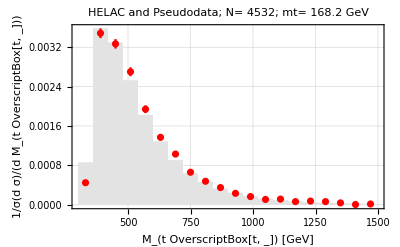
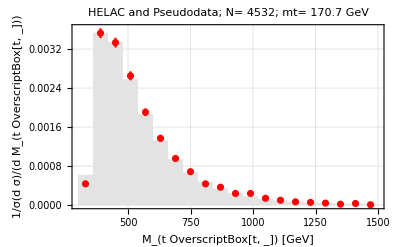
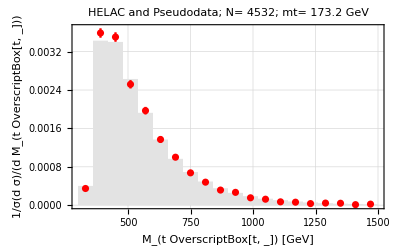
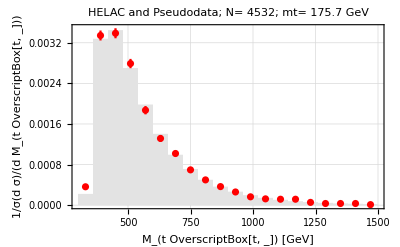
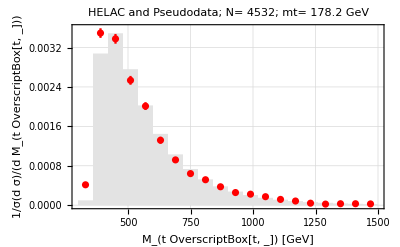

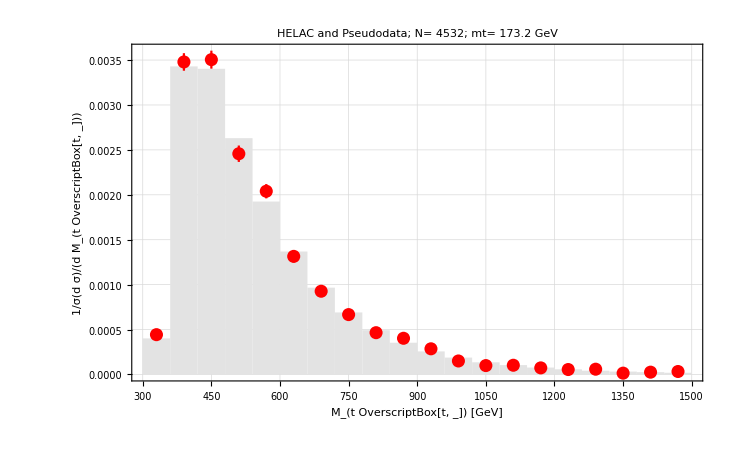

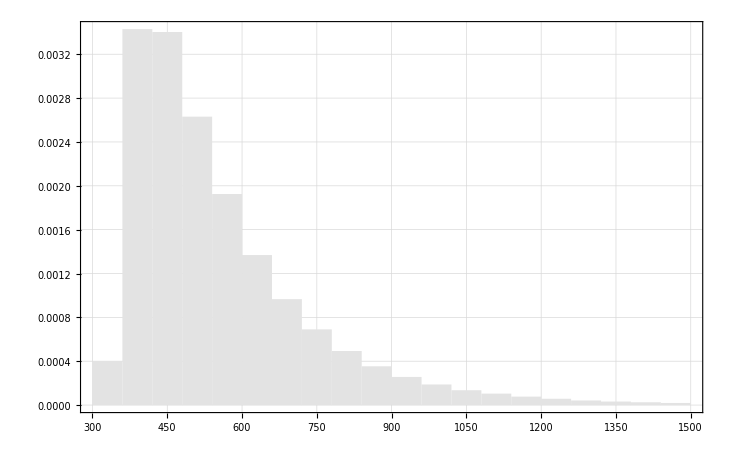

{0.000401329,0.00342916,0.00340265,0.00263054,0.00192488,0.00136844,0.000966112,0.000690271,0.000492851,0.000353404,0.000256462,0.000187836,0.000135379,0.000104231,0.0000770411,0.0000573083,0.0000417718,0.0000318871,0.0000256177,0.0000189035}

{0.0229479,0.206752,0.19594,0.159753,0.11474,0.0856134,0.0646514,0.0419241,0.033098,0.0225066,0.0127979,0.0110327,0.0070609,0.0070609,0.00264784,0.0033098,0.00286849,0.00198588,0.00242718,0.000882613}

{0.000424789,0.00353015,0.0034862,0.00263662,0.00193719,0.00132564,0.000930142,0.000681128,0.000443099,0.000336902,0.000223381,0.000194085,0.000102535,0.0000952114,0.0000952114,0.0000439437,0.0000366198,0.0000402818,7.32396×10^-6,0.0000256338}

```mathematica
filehel=Table[FileNames[][[i]],{i,1,nmass}];

datahel=Block[{list},
list=Reap[Do[Sow[ReadList[filehel[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahisthel[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[datahel[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossectionhel=Table[Reap[Do[Sow[datahel[[j,1]]],{j,1,nmass,1}]][[2,1,i,2]],{i,1,nmass}] (*fb*)

binshel=Partition[Block[{bin},
bin=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidthel=Table[(Max[binshel[[i]]]-Min[binshel[[i]]])/(nbins-1),{i,1,5}];
binsrealhel=Reap[Do[Sow[Chop[binshel[[i]]-binwidthel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrealhel[[i]],Max[binsrealhel[[i]]]+binwidthel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrealhel=Table[(Max[binsrealhel[[i]]]-Min[binsrealhel[[i]]])/(nbins),{i,1,nmass}];

valshel=Partition[Block[{val},
val=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnormhel=Table[valshel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

errorhel=Partition[Block[{err},
err=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnormhel=Table[errorhel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];
normalisationhel=Round[Table[Sum[valsnormhel[[j,i]],{i,1,Length[valsnormhel[[j]]]}]*binwidthel[[j]],{j,1,nmass}]]


Which[int==1,
binhelac=bins;
valhelac=valsnorm;
binhelacreal=binsreal;
errorhelac=errnorm;
,
int==2,
binhelac=binshel;
valhelac=valsnormhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrealhel;
errorhelac=errnormhel;
]

valhelac


histfromhelac[nmass_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{binhelacreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{binhelacreal[[nmass]]}]

combine[nevents_,nmass_,binw_]:=Show[histfromhelac[nmass],pseudoplot[nevents,3,binw],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]

pt5=Table[combine[stdnevents,i,(binwidth[[i]]*nbins/npseudobin)],{i,1,nmass}]
pt1=combine[Round[stdnevents],3,(binwidth[[3]]*nbins/npseudobin)]
histhelac=histfromhelac[3]
valhelac[[3]]
histogramlistnorm[stdnevents,3,binwidth[[3]]][[2]]
pseudopointy[stdnevents,3,binwidth[[3]]]
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidthel[[1]]*nbins/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidthel[[1]]*nbins/npseudobin);

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,nmass,1}]][[2,1]]; (*for graph*)
valsbindatanozero=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,nmass}];
Sow[DeleteCases[valerr,nol]]]][[1]];
valsnormtheo[[17]]

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,nmass,1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,nmass}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];
```

{0.00237422,0.00251199,0.00250631,0.0027122,0.0028763}

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=If[MemberQ[Flatten[Transpose[valsnormtheo]],0.]==False,{"nothing"},
Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,nmass,1},{j,1,nbins,1}]
][[2]];
all=Flatten[Table[{Range[nmass][[i]],Range[nbins][[j]]},{i,1,nmass},{j,1,nbins}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
]
```

{nothing}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value=Reap[Do[Sow[valsbintheonozero[[i]][[All,1]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
err=Reap[Do[Sow[valsbintheonozero[[i]][[All,2]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];

(*value1=Reap[Do[Sow[valsbintheonozero[[i]][[All,1]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
err1=Reap[Do[Sow[valsbintheonozero[[i]][[All,2]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
value=Table[Cases[value1[[i]],Except[value1[[i,3]]]],{i,1,Length[value1]}];
err=Table[Cases[err1[[i]],Except[err1[[i,3]]]],{i,1,Length[err1]}];*)



fitting=Which[valhelac==valsnorm,
LinearModelFit[value[[#]],fit1,x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]],
valhelac==valsnormhel,
LinearModelFit[value[[#]],fit2,x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]]
];


(*fitting=LinearModelFit[value[[#]],{x,x^2,x^3,x^4},x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]];*)
```

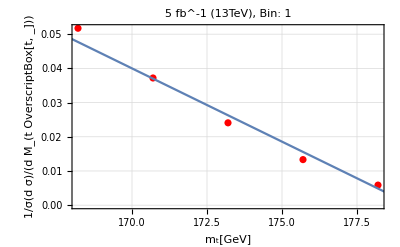
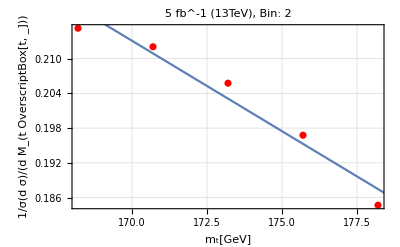
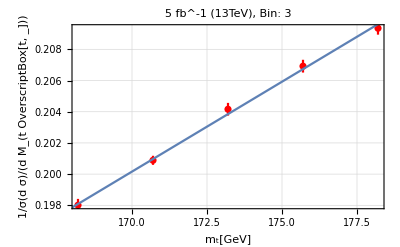
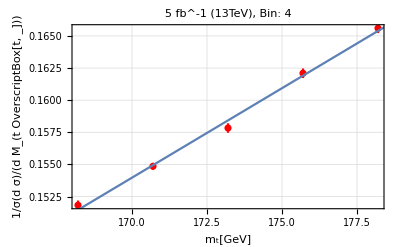
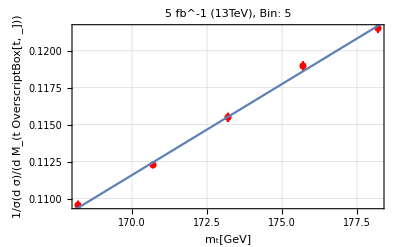
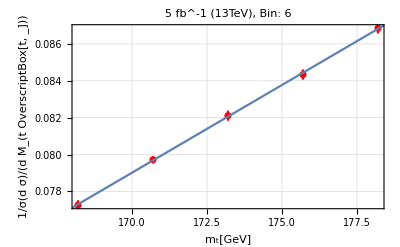
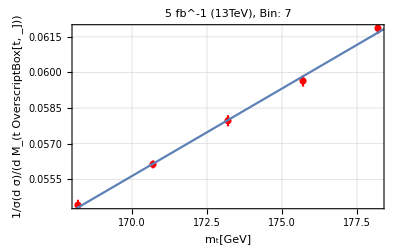
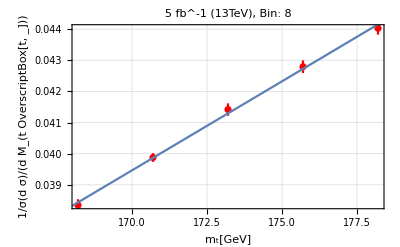

-Graphics-

-Graphics-

-0.00548129+0.000046662 x

```mathematica
valsbinplot[int_]:=ErrorListPlot[valsbindatanozero[[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_]:=Normal[fitting[[int]]]
funcbin[int_,nmass_]:=funcfit[int]/.x-> mass[[nmass]]
combbinfunc[int_]:=Block[{func},
func=funcfit[int]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit=Table[combbinfunc[i],{i,1,Length[value]}]
allfit[[8]]
allfit[[17]]
funcfit[17]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormpseudo[nevents_]:=
Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]] (*length value=non zero bins total*)
]
]
]

errnormpseudo[nevents_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,errpseudo,
MemberQ[nonzerobin,Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]]
]
]
]

PSEUDODATA USED FOR GENERATING THE CHISQUARE;
valuep1=valsnormpseudo[stdnevents][[number]];
errorp1=errnormpseudo[stdnevents][[number]];(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)
zeropost=Position[errorp1,0.]; 
errorp=Delete[errorp1,zeropost]
valuep=Delete[valuep1,zeropost]
```

{0.0025236,0.00594963,0.00589099,0.00546134,0.0047958,0.00408487,0.00338323,0.00310233,0.00253257,0.00209704,0.00183682,0.00148262,0.00136623,0.00119946,0.00115904,0.000760119,0.000658501,0.000491035,0.000694044,0.000439243}

{0.0261465,0.206536,0.204778,0.152704,0.116011,0.0826142,0.057786,0.0424057,0.0287831,0.019555,0.0177972,0.0120845,0.00725072,0.00549297,0.00527325,0.00219719,0.00241691,0.00241691,0.00241691,0.00109859}

```mathematica
THE χ^2 PROCEDURE;
```

173.092

173.092

1.56215

{170.786,175.397}

2.30528

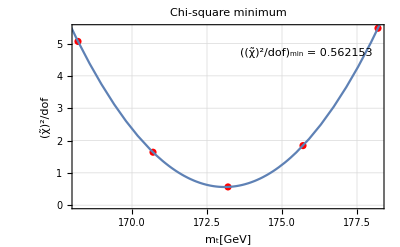

173.092±2.30528

0.0777967

{0.00305197,0.336211,0.0248399,1.09694,0.0100273,0.0185516,0.00386319,0.128521,0.0649263,0.661882,1.68927,0.244971,0.536151,0.294314,0.351333,2.7641,0.0777967,0.859306,1.55693,0.0092715}

{5.06449,1.63836,0.564368,1.84252,5.47281}

0.0262859

0.0240797

0.0261465

0.53197

6.36855×10^-6

83530.7

5747.04

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_]:=(pvalue[[int]]-fitting[[int]][mass])^2/(perror[[int]]^2);
sumchisquare[pvalue_,perror_,mass_]:=Sum[chisquarebin[pvalue,perror,i,mass],{i,1,Length[pvalue]-1}];
chitilde[pvalue_,perror_,mass_]:=sumchisquare[pvalue,perror,mass]/(Length[pvalue]-1)
minchitilde[pvalue_,perror_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x],{x,168.2,178.2}]]
chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]]],{i,1,nmass}][[j]]},{j,1,nmass}];
chifunc=LinearModelFit[chidata,{1,x,x^2},x];
minimumx=minchitilde[valuep,errorp]
x/.Last[FindMinimum[{Normal[chifunc],162.8≤ x≤ 178.2},{x,168.2}]]
chivaluebnd=chitilde[valuep,errorp,minimumx]+1
(*deltamassbound=x/.Solve[chitilde[valuep,errorp,x]==chivaluebound,x]*) (*finding the corresponding m value for given chi square value without divide by dof*)
deltamassbnd=x/.Solve[Normal[chifunc]==chivaluebnd,x]
deltam1=Mean[Abs[minimumx-deltamassbnd]]
chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[chitilde[valuep,errorp,minimumx]]],Background->White],Scaled[{.75,.85}]]]
PlusMinus[minimumx,deltam1]

chisquarebin[valuep,errorp,17,mass[[3]]]
Table[chisquarebin[valuep,errorp,i,mass[[3]]],{i,1,Length[valuep]}]
Table[chitilde[valuep,errorp,mass[[i]]],{i,1,5}]
fitting[[1]][173.2]
value[[1,3,2]]
valuep[[1]]

(fitting[[1]][3]-valuep[[1]])^2
errorp[[1]]^2

(fitting[[1]][3]-valuep[[1]])^2/(errorp[[1]]^2)
sumchisquare[valuep,errorp,3]/18
```

```mathematica
BEFORE DIVIDED BY DEGREE OF FREEDOMS (EXTRACTING ONE DELTA MASS);
```

173.092

11.6809

{172.563,173.62}

{0.528867,-0.528867}

0.528867

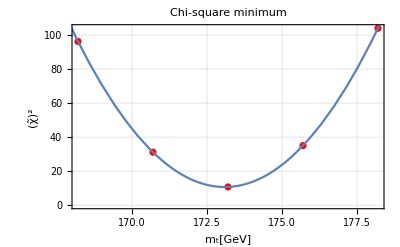

173.092±0.528867

```mathematica
minchitilderaw[pvalue_,perror_]:=x/.Last[FindMinimum[sumchisquare[pvalue,perror,x],{x,168.2,178.2}]]
mmiddle=minchitilderaw[valuep,errorp]
chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]]],{i,1,nmass}][[j]]},{j,1,nmass}];
chifuncraw=LinearModelFit[chidataraw,{1,x,x^2},x];
chivaluebound=sumchisquare[valuep,errorp,mmiddle]+1
(*deltamassbound=x/.Solve[chitilde[valuep,errorp,x]==chivaluebound,x]*) (*finding the corresponding m value for given chi square value without divide by dof*)
deltamassbound=x/.Solve[Normal[chifuncraw]==chivaluebound,x]
mmiddle-deltamassbound
deltamone=Mean[Abs[mmiddle-deltamassbound]]
chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"]
PlusMinus[mmiddle,deltamone]
```

{167.513,170.382,174.153,176.14,178.388}

{0.640104,0.576763,0.447178,0.42074,0.229996}

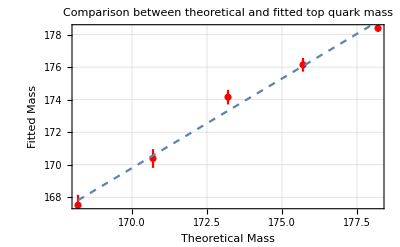

```mathematica
FITTED MASS ;
EXTRACTION OF MASS AND DELTA MASS OF TOP QUARK FOR ONE PSEUDO EXPERIMENTS;
fittingmass[nevents_,m_]:=Reap[
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,result,chisqraw,datachiraw,fchiraw,chibound,deltambound,deltameins,fchi},
pvaluelist=valsnormpseudo[nevents][[m]];
perrorlist=errnormpseudo[nevents][[m]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
chisqraw=ParallelTable[sumchisquare[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
datachiraw=ParallelTable[{mass[[j]],chisqraw[[j]]},{j,1,nmass}];
fchiraw=LinearModelFit[datachiraw,{1,x,x^2},x];
(*fchi=Fit[datachi,{1,x,x^2},x];
mout=x/.Last[FindMinimum[{Normal[fchiraw],162.8≤ x≤ 178.2},{x,168.2}]];*)
mout=minchitilderaw[pvaluelist,perrorlist];
chibound=sumchisquare[pvaluelist,perrorlist,minchitilderaw[pvaluelist,perrorlist]]+1;
deltambound=x/.Solve[Normal[fchiraw]==chibound,x];
deltameins=Mean[Abs[mout-deltambound]];
result=Sow[{mout,deltameins}]
]
][[2,1]];

massfit=Reap[Do[Sow[fittingmass[stdnevents,i]],{i,1,nmass,1}]][[2,1]];
masschi=Reap[Do[Sow[Flatten[massfit[[i]],1]],{i,1,nmass,1}]][[2,1]];
fitmass=masschi[[All,1]]
fitmasserr=masschi[[All,2]]

PLOTTING THE THEORETICAL MASS AND THE MASS FROM CHI SQUARE + 1 ANALYSIS  FROM ONE PSEUDO EXPERIMENTS(NO BIASED);
fitmassplot=ErrorListPlot[Table[{{mass[[i]],fitmass[[i]]},ErrorBar[fitmasserr[[i]]]},{i,1,nmass}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],fitmass[[i]]},{i,1,nmass}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,n_]:=Partition[Reap[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,zeropos,chisq,datachi,fchi,mout,chisqmin,result,pvalue},
pvaluelist=valsnormpseudo[nevents][[number]];
perrorlist=errnormpseudo[nevents][[number]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
(*fchi=Fit[datachi,{1,x,x^2},x];
mout=x/.Last[FindMinimum[{fchi,162.8≤ x≤ 178.2},{x,168.2}]];*)
mout=minchitilderaw[pvaluelist,perrorlist];
chisqmin=chitilde[pvaluelist,perrorlist,mout];
pvalue=ChiSquarePValue[chisqmin*(Length[pvaluelist]-1),(Length[pvaluelist]-1)][[2]];
result=Sow[{mout,chisqmin,pvalue}]
]
];
][[2,1]],n];
exp=Reap[Sow[npseudoexp[stdnevents,npseudo]]][[2,1,1,1]];
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

{0.302948,0.315486,0.452602,0.457809,0.516985,0.526865,0.545687,0.54576,0.571082,0.630484,0.646212,0.649309,0.656665,0.677308,0.685726,0.690036,0.702945,0.749746,0.761958,0.762888,0.771126,0.788915,0.790175,0.795282,0.803331,0.812776,0.823066,0.823083,0.827949,0.835258,0.841662,0.856369,0.857975,0.87238,0.903823,0.914274,0.917753,0.955908,0.966251,0.975408,0.97567,0.980872,0.983472,0.993056,0.994065,0.996528,0.997599,1.03351,1.04138,1.0695,1.07905,1.09015,1.11173,1.11174,1.11477,1.11704,1.13518,1.13782,1.14776,1.15175,1.17066,1.19541,1.19638,1.19987,1.21733,1.24059,1.24492,1.25067,1.25278,1.27275,1.27647,1.28405,1.28766,1.314,1.3226,1.33334,1.34433,1.34437,1.3474,1.34952,1.43343,1.44526,1.45627,1.46454,1.46873,1.48463,1.48664,1.49175,1.51404,1.534,1.58362,1.61908,1.62735,1.64741,1.6752,1.68406,1.69257,1.74885,1.81725,2.15747}

20

{{173.937,0.302948},{173.692,0.315486},{173.571,0.452602},{173.438,0.457809},{173.802,0.516985},{173.418,0.526865},{173.85,0.545687},{174.271,0.54576},{172.465,0.571082},{173.96,0.630484},{172.566,0.646212},{173.255,0.649309},{173.239,0.656665},{173.409,0.677308},{173.439,0.685726},{173.581,0.690036},{173.124,0.702945},{173.536,0.749746},{173.344,0.761958},{173.636,0.762888},{174.662,0.771126},{173.735,0.788915},{174.154,0.790175},{173.628,0.795282},{173.361,0.803331},{174.214,0.812776},{173.514,0.823066},{173.773,0.823083},{173.226,0.827949},{173.242,0.835258},{174.147,0.841662},{173.749,0.856369},{173.829,0.857975},{173.409,0.87238},{173.903,0.903823},{173.739,0.914274},{173.912,0.917753},{173.768,0.955908},{173.853,0.966251},{173.933,0.975408},{173.423,0.97567},{173.519,0.980872},{173.534,0.983472},{173.981,0.993056},{173.375,0.994065},{173.182,0.996528},{173.086,0.997599},{174.305,1.03351},{173.528,1.04138},{173.03,1.0695},{173.424,1.07905},{174.265,1.09015},{172.951,1.11173},{174.002,1.11174},{173.979,1.11477},{173.761,1.11704},{173.582,1.13518},{173.64,1.13782},{173.3,1.14776},{173.609,1.15175},{173.202,1.17066},{173.633,1.19541},{173.133,1.19638},{173.967,1.19987},{173.412,1.21733},{173.775,1.24059},{173.803,1.24492},{174.034,1.25067},{173.437,1.25278},{173.74,1.27275},{174.456,1.27647},{173.415,1.28405},{173.36,1.28766},{172.787,1.314},{173.353,1.3226},{173.934,1.33334},{172.919,1.34433},{174.086,1.34437},{174.659,1.3474},{173.294,1.34952},{173.504,1.43343},{173.454,1.44526},{173.587,1.45627},{173.169,1.46454},{172.898,1.46873},{174.009,1.48463},{173.369,1.48664},{173.069,1.49175},{173.383,1.51404},{172.805,1.534},{173.37,1.58362},{174.527,1.61908},{173.418,1.62735},{172.108,1.64741},{172.959,1.6752},{173.427,1.68406},{172.825,1.69257},{174.029,1.74885},{173.469,1.81725},{173.972,2.15747}}

100

173.565

{0.00542916,0.0159451,0.0164149,0.0217982,0.0296152,0.0309139,0.0370379,0.0437171,0.0464297,0.0511807,0.0615959,0.0630812,0.0674606,0.0705881,0.0750806,0.0963777,0.110942,0.12615,0.127312,0.127322,0.127991,0.138074,0.140728,0.141856,0.146752,0.147021,0.150067,0.152869,0.155806,0.156319,0.170077,0.17394,0.174422,0.181949,0.183633,0.19062,0.194817,0.195836,0.19595,0.203301,0.203758,0.204742,0.207393,0.209789,0.211723,0.220822,0.237088,0.237609,0.264259,0.265401,0.271243,0.285327,0.287657,0.310277,0.323205,0.326179,0.337575,0.338782,0.347062,0.362927,0.367761,0.368912,0.372017,0.383085,0.395012,0.396618,0.402221,0.407208,0.414225,0.415946,0.432435,0.43723,0.441366,0.443972,0.464086,0.468988,0.479226,0.496308,0.520826,0.535386,0.581407,0.588735,0.605707,0.614212,0.646028,0.649089,0.666648,0.699565,0.705655,0.740236,0.740486,0.759761,0.777717,0.890777,0.961741,0.998851,1.09399,1.09656,1.10002,1.4569}

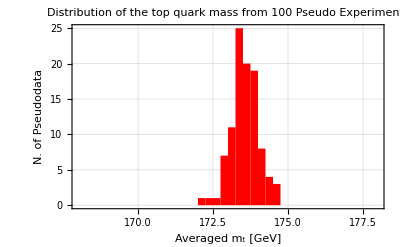

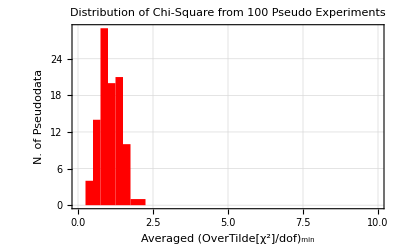

19

1.07721

OneSidedPValue→0.364697

True

Theory, LO QCD | Variable | Luminosity [fb^-1] | m_t±δm_t[GeV] | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=E_T/2 | M_(t OverscriptBox[t, _]) | 5 | 173.565±0.407208 | 1.07721 | 0.366983 | -0.365127

```mathematica
(*pexpmass=Delete[Sort[exp[[All,1]]],Partition[(-1)*Range[11],1]]; (*96 percent of the mass data *)
pexpchisq=Delete[Sort[exp[[All,2]]],Partition[(-1)*Range[11],1]] (*96 percent of the chi square min data due to isolated big value of chi*)*)

pexpchisq=Sort[exp[[All,2]]]

ELIMINATE THI  CHI-SQUARE THAT IS MORE THAN CHI SQUARE STANDARD FOR ET2;
chistandard=20
newexp=Reap[Do[
Which[scalename[[k]]=="et2",
If[(pexpchisq[[i]]<chistandard)&&(pexpchisq[[i]]==exp[[j,2]]),Sow[{exp[[j,1]],exp[[j,2]]}],Nothing],
scalename[[k]]=="mt",
Nothing],
{k,1,Length[scalename],1},{i,1,Length[pexpchisq],1},{j,1,Length[exp],1}]][[2,1]]
Length[newexp]
pexpmass=newexp[[All,1]];
pexpchis=newexp[[All,2]];


massout=Mean[pexpmass]

stddeviations=Reap[Do[
Sow[StandardDeviation[exp[[All,1]]]],
{i,1,Length[exp],1}]][[2,1]];

deltamassout=Reap[Block[{sortedmass,variance},
sortedmass=pexpmass;
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Print[variance];
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]][[2,1,1]];

chiout=Mean[pexpchis];


pexpmasshist=Histogram[pexpmass,{168,178,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from " <>ToString[Length[pexpchis]]<>" Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchis,{0,10,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from "<>ToString[Length[pexpchis]]<>" Pseudo Experiments"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout*(Length[pvalue]-1),Length[pvalue]-1][[2]];
pvout=pvalue[valuep];
Length[valuep]-1
chiout
ChiSquarePValue[1.06*3,3]
(*pvout=Mean[Sort[exp[[All,3]]]]*)
pvout>pvaluestandard
(*stddeviations=(Abs[massout[[number]]]*Sqrt[Length[pexpmass]/2])/InverseErfc[pvout]*10^-3*)
deltam=mass[[number]]-massout;
result=Grid[{{"Theory, LO QCD", "Variable","Luminosity [fb^-1]",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm]<>"[GeV]", "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{StringForm["Full, μ_0=``",scale[[int]]],variable[[numbofdiffdist]],luminosity,PlusMinus[N[massout,2],N[deltamassout,2]],chiout,pvout ,deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudodata.pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_mass_fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_result_table.pdf", result];*)
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_"<>ToString[fitname]<>"_fitting_each_bin.pdf", allfit];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_"<>ToString[fitname]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_hist.pdf", histhelac];*)
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_"<>ToString[fitname]<>"_fitting_idv_1.pdf", allfit[[1]]];*)
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_"<>ToString[fitname]<>"_parabola_chi_square.pdf",chiparabola]*)
```

```mathematica
GATHERING DATA;
(*If[luminosity==5,
Do[
Export["kdata_"<>ToString[varname[[numbofdiffdist]]]<>"_"<>ToString[nbins]<>"_"<>massname[[i]]<>"_"<>scalename[[int]]<>".txt",Transpose[{bins[[i]],valhelac[[i]]}],"Table"],
{i,1,nmass,1}
],
Nothing
]*)
```